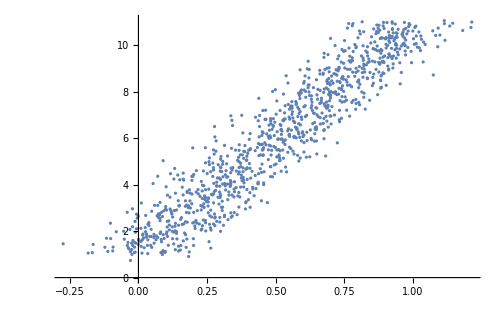

```mathematica
n=1000;
data=Transpose[{Range[n]/n,10 Range[n]/n+1}]+0.1 RandomVariate[NormalDistribution[],{n,2}];
ListPlot[data,ImageSize->500]
```

```mathematica
Clear[f,iter,gradsp,v,eps,nu,xMatr,yVector,a,x,y]
xMatr=Transpose@{ConstantArray[1,n],data⟦All,1⟧};
yVector=data⟦All,2⟧;


v={0,0};(*вектор переменных*)
eps=0.000001;(*приближение*)
nu=0.01;(*шаг*)
iter=1000;(*кол-во итераций*)
```

```mathematica
f[x_,y_]:=1/n Total[yVector-(xMatr.{x,y})].xMatr
```

```mathematica
gradsp[v_,eps_,nu_,iter_,yVector_,xMatr_,n_]:=Module[{v1=v,v2=v,x,y,i=1,lst={},gr},
gr=-((yVector-(xMatr.v1)).xMatr)/n;
v2=v1-nu*gr;
AppendTo[lst,v2];
While[Norm[v2-v1]>eps&&i≤iter,v1=v2;
gr=-((yVector-(xMatr.v1)).xMatr)/n;
v2=v1-nu*gr;
AppendTo[lst,v2];i++];
lst]
```

```mathematica
res=gradsp[v,eps,nu,iter,yVector,xMatr,n]⟦-1⟧
```

{3.15855,5.91536}

```mathematica
listtForDg=Transpose@{data⟦All,1⟧,(data⟦All,1⟧*res⟦2⟧+res⟦1⟧)};
```

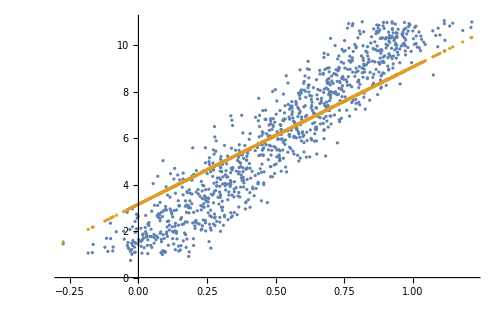

```mathematica
ListPlot[{data,listtForDg},ImageSize->500]
```